# Assignment 3

## Mortar Simulation

Load files.

```mathematica
SetDirectory["C:\\Users\\brook\\Documents\\Workspaces\\CSC 450\\CSC450\\assignment3"]
FileNames[]
```

C:\Users\brook\Documents\Workspaces\CSC 450\CSC450\assignment3

{a3_notebook.nb,a3_p1_f1_1D.csv,a3_p1_f1.csv,a3_p1_f1_ground.csv,a3_p1_f2_1D.csv,a3_p1_f2.csv,a3_p1_f2_ground.csv,a3_p1_f3.csv,a3_p1_f4.csv,a3_p1_f5_1D.csv,a3_p1_f5.csv,a3_p1_f5_ground.csv,a3_p1_f6.csv,Mathematica.md,output1_b.csv,output3_f10.csv,output3_f11.csv,output3_f12.csv,output3_f6.csv,output3_f7.csv,output3_f8.csv,output3_f9.csv,output3_p4_1.csv,output3_p4_2.csv,output3_p4_3.csv,output3_p4_4.csv,output3_p4_5.csv,output3_p4_a.csv,output3_p4_b.csv,output3_p4_c.csv,output3_p4_d.csv,output3_p4_e.csv,output3_p4_f.csv,output3_p4_g.csv}

## Example 1

The ground is defined with an ND polynomial function, a sub-class of FunctionND. This one is a flat ground for a simple example. It’s given an azimuth angle of PI/4 and an elevation angle also of PI/4. It’s magnitude of velocity is 10. 
With this information, we create a ProjectileND object. It’s Vx, Vy, Vz are computed and then we run the simulate method to calculate the trajectory and write to a CSV file. 

There’s 2 implementations of this method, one in 3D and one in 1D.

### 3D Simulation

Starting at its initial position, step through with time and calculate the position of the Mortar M(t), located at X(t), Y(t), Z(t). These values are calculated and returned in a position array.
This is done until the Z position is <=  to the ground’s Z, meaning the projectile has hit the ground.

We can decrease the step size to produce more accurate results, but for that I’ll be using the 1D implementation. This simulation is just for demonstration and clarity purposes.

Below a define a function I’ll use for plotting the trajectory from a CSV file produced from the simulation method as well as a function used for the ground.

```mathematica
plotDataWithGround[filename_String,groundFunction_]:=Module[{data,xValues,yValues,zValues,pointsPlot,groundPlot},
(*Import the CSV file*)data=Import[filename,"CSV"];
(*Remove the header row*)data=Rest[data];
(*Separate the data into x,y,and z values*)
xValues=data[[All,1]];
yValues=data[[All,2]];
zValues=data[[All,3]];
(*Create a 3D plot of the data*)pointsPlot=ListPointPlot3D[data,PlotStyle->PointSize[0.02]];
(*Create a 3D plot of the ground function*)groundPlot=Plot3D[groundFunction[x,y],{x,Min[xValues],Max[xValues]},{y,Min[yValues],Max[yValues]}];
(*Show both plots together*)Show[pointsPlot,groundPlot,PlotLabel->"Ground Function: "<>ToString[groundFunction]]]
```

The shell lands after  t = 1.44s at about (7.19, 7.19, 0).

```mathematica
plotDataWithGround["a3_p1_f1.csv",Function[{x,y},0]]
```

-Graphics3D-

This graph shows the x,y,z movement of the projectile over a flat ground.

### 1D Simulation

The 1D visualization of the one above. From the same class, there is a 1D simulation function where we can compute the trajectory with a Function1D object by Z from the 3D projectile object from the ground height.

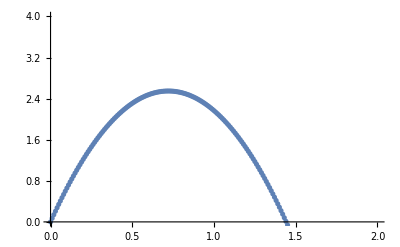

```mathematica
(*Import the data from the CSV file*)
data=Import["a3_p1_f1_1D.csv","CSV"];

(*Remove the header row*)
data=Rest[data];

ListPlot[data,PlotRange->{{0,2},{0,4}}]
```

This graph shows only the Z trajectory of the projectile over time.

### 1D from ND Simulation

An even more direct solution in 1D than the previous example is V2 of the mortar problem. This uses a Function1DFromND class. I made it an abstract class and implemented the func method separately to be consistent with the rest of my projectile classes I’ve created.
I create a PolynomialND object to represent the ground just as before; then this time I create a Function1DFromND object to represent the projectile. Then I create an anonymous Function1D as before who’s func method can find the projectile’s current height - the ground height .

In order to create the 1D simulation, we step through u, solving the function 1D and writing to a CSV.

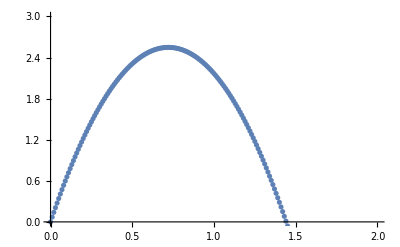

```mathematica
(*Import the data from the CSV file*)
data=Import["a3_p1_f3.csv","CSV"];

(*Remove the header row*)
data=Rest[data];

ListPlot[data,PlotRange->{{0,2},{0,3}}]
```

Identical to the last graph using a more direct implementation strictly for 1D.

## Example 2

This example has the same azimuth and trajectory angles as before but a velocity magnitude of 40. It’s ground function is f(x,y) = 1/4x + 1/4y.

The projectile lands at about t = 5.67 at (56.70,  98.21, 38.72)

### 3D Simulation

```mathematica
plotDataWithGround["a3_p1_f2.csv",Function[{x,y},0.25x+0.25y]]
```

-Graphics3D-

### 1D (Function1DFromND) Simulation

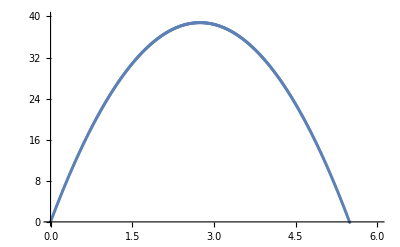

```mathematica
(*Import the data from the CSV file*)
data=Import["a3_p1_f4.csv","CSV"];

(*Remove the header row*)
data=Rest[data];

ListPlot[data,PlotRange->{{0,6},{0,40}}]
```

## Example 3

This example has the same azimuth and trajectory angles as before but a velocity magnitude of 40. It’s ground function is f(x,y) = 1/4x + 1/4y.

The projectile lands at about t = 4.995s at (6.30, 10.91, 19.88).

### 3D Simulation

This is a different function that allows me to test and visualize more complex ground functions without defining them in Mathematica.

```mathematica
(*Import the CSV files*)data=Import["a3_p1_f5.csv","CSV"];
groundData=Import["a3_p1_f5_ground.csv","CSV"];

(*Remove the header row*)
data=Rest[data];

(*Separate the data into x,y,and z values*)
xValues=data[[All,1]];
yValues=data[[All,2]];
zValues=data[[All,3]];
(*Separate the ground data into x,y,and z values*)
xGroundValues=groundData[[All,1]];
yGroundValues=groundData[[All,2]];
zGroundValues=groundData[[All,3]];

(*Create a 3D plot of the data*)
pointsPlot=ListPointPlot3D[data,PlotStyle->PointSize[0.02]];
(*Create a 3D plot of the ground data*)
groundPlot=ListPointPlot3D[groundData,PlotStyle->PointSize[0.02]];

(*Show both plots together*)
Show[pointsPlot,groundPlot]
```

-Graphics3D-

### 1D (Function1DFromND) Simulation

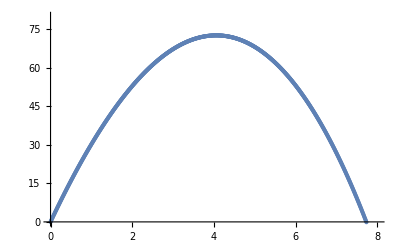

```mathematica
(*Import the data from the CSV file*)
data=Import["a3_p1_f6.csv","CSV"];

(*Remove the header row*)
data=Rest[data];

ListPlot[data,PlotRange->{{0,8},{0,80}}]
```